```mathematica
w[i_] :=Exp[-(B+i a) ^2/(2W)]
```

```mathematica
w[2]
```

ⅇ^(-(2 a+B)^2/(2 W))

```mathematica
ρ[p_] := 1/Sqrt[2 π Vg] Exp[-(B+2p a)^2/(2Vg)]
```

```mathematica
wBar[i_] := Integrate[w[i] ρ[p],{B, -Infinity, Infinity}]
```

```mathematica
wBar[0]
```

ConditionalExpression[(ⅇ^(-(2 a^2 p^2)/(Vg+W)))/(√Vg √(1/Vg+1/W)), Re[1/Vg+1/W]>0]

```mathematica
wBar[1]
```

ConditionalExpression[(ⅇ^(-(a^2 (1-2 p)^2)/(2 (Vg+W))))/(√Vg √(1/Vg+1/W)), Re[1/Vg+1/W]≥0]

```mathematica
meanFit=(1-p)^2 wBar[0] + 2p(1-p)wBar[1] + p^2 wBar[2]
```

ConditionalExpression[(ⅇ^(-(2 a^2 p^2)/(Vg+W)) (1-p)^2)/(√Vg √(1/Vg+1/W))+(2 ⅇ^(-(a^2 (1-2 p)^2)/(2 (Vg+W))) (1-p) p)/(√Vg √(1/Vg+1/W))+(ⅇ^(-(2 a^2 (-1+p)^2)/(Vg+W)) p^2)/(√Vg √(1/Vg+1/W)), Re[1/Vg+1/W]>0]

```mathematica
ConditionalExpression[(ⅇ^(-(2 a^2 p^2)/(Vg+W)) (1-p)^2)/(√Vg √(1/Vg+1/W))+(2 ⅇ^(-(a+2 a p)^2/(2 (Vg+W))) (1-p) p)/(√Vg √(1/Vg+1/W))+(ⅇ^(-(2 a^2 (1+p)^2)/(Vg+W)) p^2)/(√Vg √(1/Vg+1/W)), Re[1/Vg+1/W]>0&&((Re[1/Vg+1/W]==0&&Re[a ((2 p)/Vg-2/W)]<0&&Re[a (-p/Vg+1/W)]<0)||Re[1/Vg+1/W]>0)&&((Re[1/Vg+1/W]==0&&Re[a ((2 p)/Vg-1/W)]<0&&Re[a (-(2 p)/Vg+1/W)]<0)||Re[1/Vg+1/W]>0)]
```

```mathematica
D[meanFit,p]
```

ConditionalExpression[-(2 ⅇ^(-(2 a^2 p^2)/(Vg+W)) (1-p))/(√Vg √(1/Vg+1/W))+(2 ⅇ^(-(a+2 a p)^2/(2 (Vg+W))) (1-p))/(√Vg √(1/Vg+1/W))+(2 ⅇ^(-(2 a^2 (1+p)^2)/(Vg+W)) p)/(√Vg √(1/Vg+1/W))-(2 ⅇ^(-(a+2 a p)^2/(2 (Vg+W))) p)/(√Vg √(1/Vg+1/W))-(4 a^2 ⅇ^(-(2 a^2 p^2)/(Vg+W)) (1-p)^2 p)/(√Vg √(1/Vg+1/W) (Vg+W))-(4 a^2 ⅇ^(-(2 a^2 (1+p)^2)/(Vg+W)) p^2 (1+p))/(√Vg √(1/Vg+1/W) (Vg+W))-(4 a ⅇ^(-(a+2 a p)^2/(2 (Vg+W))) (1-p) p (a+2 a p))/(√Vg √(1/Vg+1/W) (Vg+W)), ]

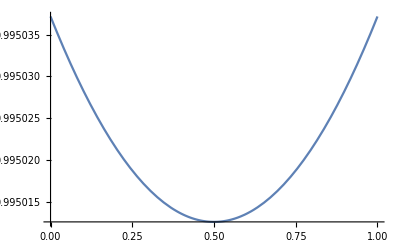

```mathematica
Plot[meanFit /.{a -> 0.01, Vg->0.01,W->1 },{p,0,1}]
```

```mathematica
meanFit /.{a -> 0.01, Vg->0.01,W->1 }
```

0.995037 ⅇ^(-0.00019802 p^2) (1-p)^2+1.99007 ⅇ^(-0.000049505 (1-2 p)^2) (1-p) p+0.995037 ⅇ^(-0.00019802 (-1+p)^2) p^2

```mathematica
(p(1-p))/(2 meanFit)D[meanFit,p]
```

ConditionalExpression[((1-p) p ((2 ⅇ^(-(a^2 (1-2 p)^2)/(2 (Vg+W))) (1-p))/(√Vg √(1/Vg+1/W))-(2 ⅇ^(-(2 a^2 p^2)/(Vg+W)) (1-p))/(√Vg √(1/Vg+1/W))-(2 ⅇ^(-(a^2 (1-2 p)^2)/(2 (Vg+W))) p)/(√Vg √(1/Vg+1/W))+(2 ⅇ^(-(2 a^2 (-1+p)^2)/(Vg+W)) p)/(√Vg √(1/Vg+1/W))+(4 a^2 ⅇ^(-(a^2 (1-2 p)^2)/(2 (Vg+W))) (1-2 p) (1-p) p)/(√Vg √(1/Vg+1/W) (Vg+W))-(4 a^2 ⅇ^(-(2 a^2 p^2)/(Vg+W)) (1-p)^2 p)/(√Vg √(1/Vg+1/W) (Vg+W))-(4 a^2 ⅇ^(-(2 a^2 (-1+p)^2)/(Vg+W)) (-1+p) p^2)/(√Vg √(1/Vg+1/W) (Vg+W))))/(2 ((ⅇ^(-(2 a^2 p^2)/(Vg+W)) (1-p)^2)/(√Vg √(1/Vg+1/W))+(2 ⅇ^(-(a^2 (1-2 p)^2)/(2 (Vg+W))) (1-p) p)/(√Vg √(1/Vg+1/W))+(ⅇ^(-(2 a^2 (-1+p)^2)/(Vg+W)) p^2)/(√Vg √(1/Vg+1/W)))), Re[1/Vg+1/W]>0]

```mathematica
deltap = (p(1-p))/(2 meanFit)D[meanFit,p] /.{a -> 0.01, Vg->0.01,W->1 }
```

((1-p) p (1.99007 ⅇ^(-0.000049505 (1-2 p)^2) (1-p)-1.99007 ⅇ^(-0.00019802 p^2) (1-p)-1.99007 ⅇ^(-0.000049505 (1-2 p)^2) p+1.99007 ⅇ^(-0.00019802 (-1+p)^2) p+0.000394074 ⅇ^(-0.000049505 (1-2 p)^2) (1-2 p) (1-p) p-0.000394074 ⅇ^(-0.00019802 p^2) (1-p)^2 p-0.000394074 ⅇ^(-0.00019802 (-1+p)^2) (-1+p) p^2))/(2 (0.995037 ⅇ^(-0.00019802 p^2) (1-p)^2+1.99007 ⅇ^(-0.000049505 (1-2 p)^2) (1-p) p+0.995037 ⅇ^(-0.00019802 (-1+p)^2) p^2))

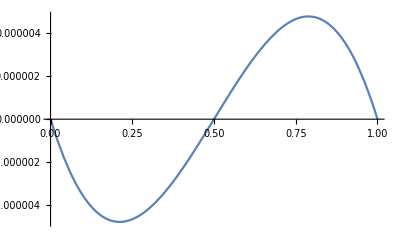

```mathematica
Plot[deltap,{p,0,1}]
```

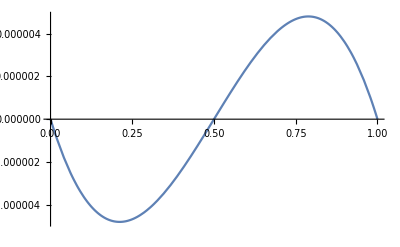

```mathematica
Plot[-a^2/(2W)p(1-p)(1-2p)/.{a -> 0.01, Vg->0.01,W->1 },{p,0,1}]
```

```mathematica
G[x_] := Exp[2Ne a^2 / W x (1-x)]
```

```mathematica
Integrate[G[y],{y,0,1}]
```

(ⅇ^((a^2 Ne)/(2 W)) √(π/2) √W Erf[(a √Ne)/(√2 √W)])/(a √Ne)

```mathematica
Integrate[G[y],{y,0,p}]
```

(ⅇ^((a^2 Ne)/(2 W)) √(π/2) √W (Erf[(a √Ne)/(√2 √W)]+Erf[(a √Ne (-1+2 p))/(√2 √W)]))/(2 a √Ne)

```mathematica
Integrate[G[y],{y,p,1}]
```

(ⅇ^((a^2 Ne)/(2 W)) √(π/2) √W (Erf[(a √Ne)/(√2 √W)]-Erf[(a √Ne (-1+2 p))/(√2 √W)]))/(2 a √Ne)

```mathematica
Integrate[G[y],{y,p,1}]/Integrate[G[y],{y,0,1}]
```

(Erf[(a √Ne)/(√2 √W)]-Erf[(a √Ne (-1+2 p))/(√2 √W)])/(2 Erf[(a √Ne)/(√2 √W)])

```mathematica
Integrate[G[y],{y,0,p}]/Integrate[G[y],{y,0,1}]
```

(Erf[(a √Ne)/(√2 √W)]+Erf[(a √Ne (-1+2 p))/(√2 √W)])/(2 Erf[(a √Ne)/(√2 √W)])

```mathematica
D[Integrate[G[y],{y,0,p}]/Integrate[G[y],{y,0,1}],p]
```

(a ⅇ^(-(a^2 Ne (-1+2 p)^2)/(2 W)) √Ne √(2/π))/(√W Erf[(a √Ne)/(√2 √W)])